```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+NabNabH[x])-2 σ[x]H[x]==0},Assumptions->ass]
```

{2 ν[x] (ψ'[x] (ν[x]^3 σ[x]+κ ν''[x])+3 κ ν'[x] ψ''[x])==6 κ ν'[x]^2 ψ'[x]+κ ν[x]^2 (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]}
```

{X1'[x]==Cos[ψ[x]] ν[x],X2'[x]==-Sin[ψ[x]] ν[x]}

```mathematica
eqν={ν''[x]==0}
```

{ν''[x]==0}

```mathematica
bcs={ψ[xmin]==ψmin,ψ[xmax]==ψmax,X1[xmin]==X1min,X2[xmin]==X2min,X1[xmax]==X1max,X2[xmax]==X2max,ν[xmin]==νmin};
```

```mathematica
σ[x_]:=σc
(*fix the gauge*)
```

```mathematica
eqψ
```

{2 ν[x] (ψ'[x] (σc ν[x]^3+κ ν''[x])+3 κ ν'[x] ψ''[x])==6 κ ν'[x]^2 ψ'[x]+κ ν[x]^2 (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
(*parameters*)
```

```mathematica
κ=1;
σc=1;
xmin=1;
xmax=3;
ψmin=-1/2;
ψmax =2.5;
X1min=0;
X2min=0;
X1max=1;
X2max=1;
νmin=1;
```

```mathematica
s=NDSolve[Flatten[{eqψ,eqX,eqν, bcs}],{ψ,X1,X2,ν},{x,xmin,xmax}][[1]]
```

{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…],ν→InterpolatingFunction[…]}

```mathematica
ν[xmin]/.s
ν[xmax]/.s
```

1.

2.77948

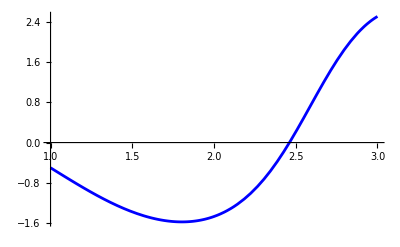

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

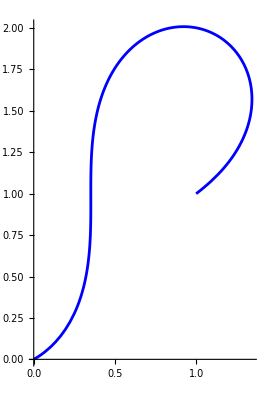

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

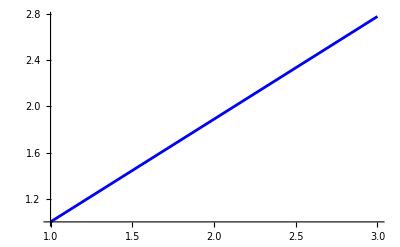

```mathematica
plotνexact=Plot[ν[x]/.s,{x,xmin,xmax},PlotStyle->Blue]
```

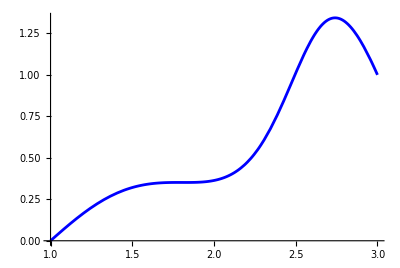

```mathematica
plotX1exact=ParametricPlot[{x,X1[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

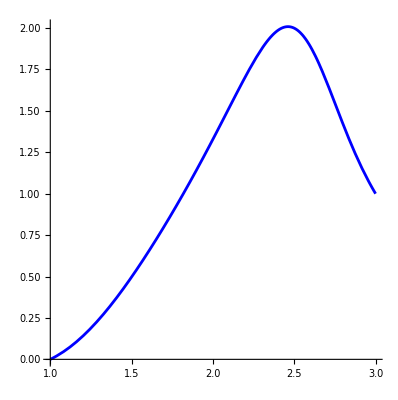

```mathematica
plotX2exact=ParametricPlot[{x,X2[x]}/.s,{x,xmin,xmax},PlotStyle->Blue]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.5},{2.9,1.96121},{2.8,1.4769},{2.7,1.06556},{2.6,0.729817},{2.5,0.462483},{2.4,0.252527},{2.3,0.0886574},{2.2,-0.0390721},{2.1,-0.138816},{2.,-0.217017},{1.9,-0.278669},{1.8,-0.327607},{1.7,-0.366759},{1.6,-0.398358},{1.5,-0.424103},{1.4,-0.44528},{1.3,-0.462853},{1.2,-0.47753},{1.1,-0.489808},{1.,-0.5}}

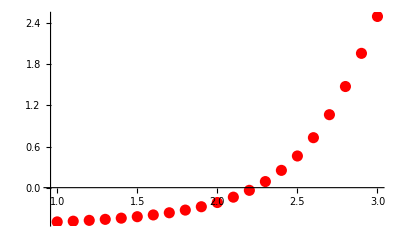

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

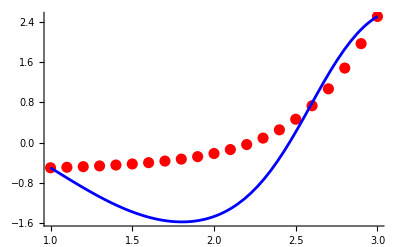

```mathematica
Show[plotψnum,plotψexact,PlotRange->Full]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{1.,1.},{1.19602,1.19172},{1.26529,1.43032},{1.21983,1.65207},{1.09494,1.82143},{0.926182,1.92877},{0.739639,1.97891},{0.551565,1.98172},{0.371163,1.94733},{0.203383,1.88425},{0.0509047,1.799},{-0.0846302,1.69626},{-0.201873,1.57918},{-0.299294,1.44959},{-0.374819,1.3081},{-0.425435,1.1541},{-0.446633,0.98547},{-0.431433,0.797961},{-0.368484,0.583713},{-0.237834,0.327927},{3.94752×10^-34,-5.82832×10^-34}}

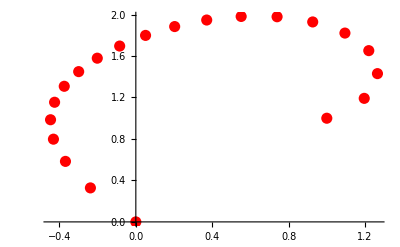

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

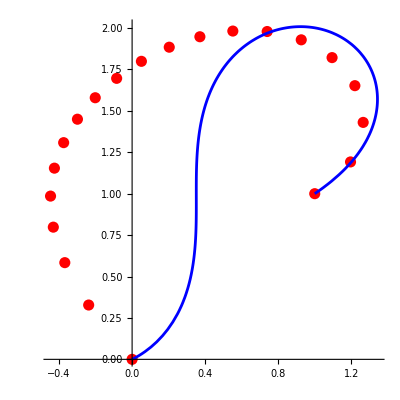

```mathematica
Show[plotXnum,plotXexact,PlotRange->Full,AspectRatio->1]
```

```mathematica
(*check ν*)
```

```mathematica
tν=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/nu.csv"];
tν=Table[{tν[[i,2]],tν[[i,1]]},{i,2,Length[tν]}]
```

{{3.,2.77948},{2.9,2.71831},{2.8,2.65574},{2.7,2.59165},{2.6,2.52594},{2.5,2.45848},{2.4,2.38911},{2.3,2.31766},{2.2,2.24395},{2.1,2.16772},{2.,2.08872},{1.9,2.00661},{1.8,1.92099},{1.7,1.83137},{1.6,1.73714},{1.5,1.63749},{1.4,1.53137},{1.3,1.41733},{1.2,1.29327},{1.1,1.15597},{1.,1.}}

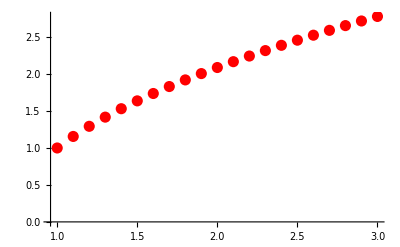

```mathematica
plotνnum=ListPlot[tν,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

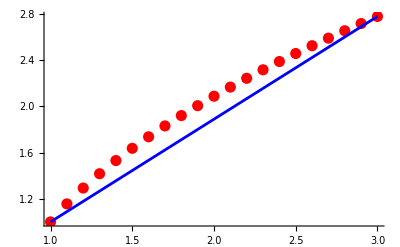

```mathematica
Show[plotνnum,plotνexact,PlotRange->Full]
```

```mathematica
(*check X1*)
```

```mathematica
tX1=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX1=Table[{tX1[[i,4]],tX1[[i,1]]},{i,2,Length[tX1]}]
```

{{3.,1.},{2.9,1.19602},{2.8,1.26529},{2.7,1.21983},{2.6,1.09494},{2.5,0.926182},{2.4,0.739639},{2.3,0.551565},{2.2,0.371163},{2.1,0.203383},{2.,0.0509047},{1.9,-0.0846302},{1.8,-0.201873},{1.7,-0.299294},{1.6,-0.374819},{1.5,-0.425435},{1.4,-0.446633},{1.3,-0.431433},{1.2,-0.368484},{1.1,-0.237834},{1.,3.94752×10^-34}}

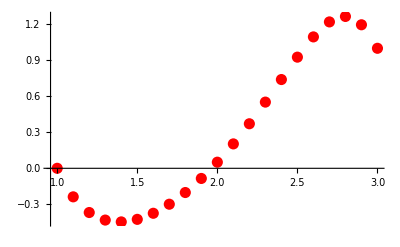

```mathematica
plotX1num=ListPlot[tX1,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

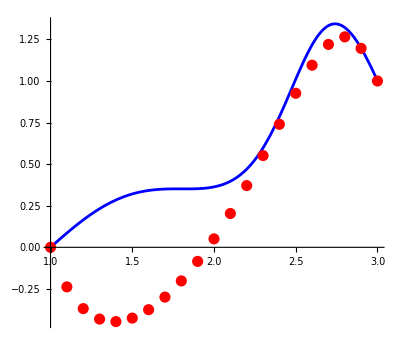

```mathematica
Show[plotX1exact,plotX1num,PlotRange->Full]
```

```mathematica
(*check X2*)
```

```mathematica
tX2=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX2=Table[{tX2[[i,4]],tX2[[i,2]]},{i,2,Length[tX2]}]
```

{{3.,1.},{2.9,1.19172},{2.8,1.43032},{2.7,1.65207},{2.6,1.82143},{2.5,1.92877},{2.4,1.97891},{2.3,1.98172},{2.2,1.94733},{2.1,1.88425},{2.,1.799},{1.9,1.69626},{1.8,1.57918},{1.7,1.44959},{1.6,1.3081},{1.5,1.1541},{1.4,0.98547},{1.3,0.797961},{1.2,0.583713},{1.1,0.327927},{1.,-5.82832×10^-34}}

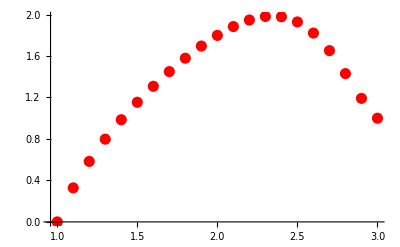

```mathematica
plotX2num=ListPlot[tX2,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

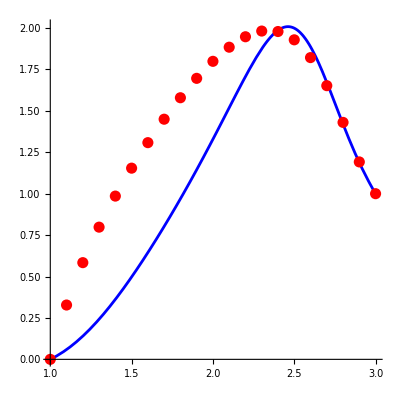

```mathematica
Show[plotX2exact,plotX2num,PlotRange->Full]
```

```mathematica
err1=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/err_1.csv"];
err1=Table[{err1[[i,2]],err1[[i,1]]},{i,2,Length[err1]}]
```

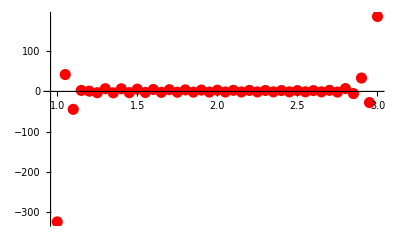

```mathematica
ListPlot[err1,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

```mathematica
err2=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/err_2.csv"];
err2=Table[{err2[[i,2]],err2[[i,1]]},{i,2,Length[err2]}]
```

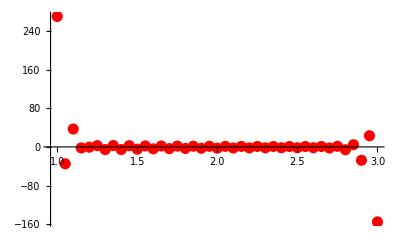

```mathematica
ListPlot[err2,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```